Notebook for 2D & 3D visualization of SPM (simulated) data stored in WSxM format together with balls and sticks model of geometry (from DFT calculations)
Possible to obtain also any line-profile from SPM data.

```mathematica
(* a way to lower down the amount of memory *)
$HistoryLength=2;
```

## Importing WSxM

```mathematica
(* importing WSxM-like files *)
path="~/WORK/pictures_calc/PTCDA_single_mol/";
f=Import[path<>"didv_-1.37733_tip_relaxed-CO_WF_5.0_eta_0.1_002.xyz","Table",HeaderLines->4];
```

```mathematica
lx=Max[f[[All,1]]]-Min[f[[All,1]]];
ly=Max[f[[All,2]]]-Min[f[[All,2]]];
max=Max[f[[All,3]]]
min=Min[f[[All,3]]]
Print["Fast view"];
ListContourPlot[f,AspectRatio->ly/lx,PlotRange->Full]
```

0.00964982002152435861

2.42647447501527801×10^-16

Fast view

-Graphics-

## Simple atoms view (balls and sticks)

### Header & Parser

```mathematica
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
pathgeom=path;(*"~/Documents/WORK/z-sshfs/tmp/VASP/";*)
filename="answer.xyz"; (* "bas","xyz","in" and CONTCAR/POSCAR files are supported at the moment *)
geomin= Import[pathgeom<>filename,"Table"];
geomin[[Range[1,20]]]//TableForm (* Just to see an example *)
```

38 |  |  |  | 
 |  |  |  | 
C | 12.1465 | 15.0065 | 1. | 6
C | 11.418 | 13.7912 | 1. | 6
C | 12.1096 | 12.5912 | 1. | 6
C | 13.5021 | 12.5804 | 1. | 6
C | 14.2642 | 13.7503 | 1. | 6
C | 13.5724 | 15.0004 | 1. | 6
C | 14.2734 | 16.2465 | 1. | 6
C | 13.5249 | 17.4215 | 1. | 6
C | 12.1357 | 17.427 | 1. | 6
C | 11.435 | 16.2303 | 1. | 6
C | 16.4345 | 15.0004 | 1. | 6
C | 15.7347 | 13.7533 | 1. | 6
C | 16.4858 | 12.5799 | 1. | 6
C | 17.8766 | 12.5775 | 1. | 6
C | 18.5743 | 13.7754 | 1. | 6
C | 17.8604 | 14.9972 | 1. | 6
C | 18.5858 | 16.215 | 1. | 6
C | 17.8928 | 17.4149 | 1. | 6

```mathematica
If[StringTake[filename,-3]=="bas",{Print["BAS file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=2,i≤maxat1+1,i++,geom[[i-1]]={geomin[[i,1]],atomicprop[[geomin[[i,1]],1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[geomin[[i,1]],2]],atomicprop[[geomin[[i,1]],4]],atomicprop[[geomin[[i,1]],5]],atomicprop[[geomin[[i,1]],6]]}];};,
If[StringTake[filename,-3]=="xyz",{Print["XYZ file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=3,i≤maxat1+2,i++,For[j=1,j≤99,j++,If[ToString[geomin[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i-2]]={j,geomin[[i,1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]==".in",{Print["FHI-AIMS in file"];aimsimport2=Array[Null,Length[geomin]];ia=1;cell={};
For[i=1,i≤Length[aimsimport2],i++,If[geomin[[i,1]]=="atom",{aimsimport2[[ia]]=geomin[[i]],ia=ia+1},If[geomin[[i,1]]=="lattice_vector",cell=Append[cell,geomin[[i,{2,3,4}]]]]]];
aimsimport2=Drop[aimsimport2,-Length[geomin]+ia-1];If[cell=={},cell=.];
xyzEx=aimsimport2[[All,{5,2,3,4}]];(*geomin=.;*)aimsimport2=.;
maxat1=Length[xyzEx];
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,For[j=1,j≤Length[atomicprop],j++,If[ToString[xyzEx[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i]]={j,xyzEx[[i,1]],xyzEx[[i,2]],xyzEx[[i,3]],xyzEx[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]=="CAR",{Print["CONTCAR/POSCAR VASP file"],(*VASP CONTCAR file *)direct=False;
If[geomin[[8,1]]=="Direct",{Print[".1dOK"],tmpn=8,direct=True},If[geomin[[9,1]]=="Direct",{Print[".1dOK"],tmpn=9,direct=True},
If[geomin[[8,1]]=="Cartesian",{Print[".1dOK"],tmpn=8},If[geomin[[9,1]]=="Cartesian",{Print[".1dOK"],tmpn=9},
{Print["problem: geomin[[8,1] = "]<>geomin[[8,1]],Print["problem: geomin[[9,1] = "]<>geomin[[9,1]]}]]]];
tmpn;cell=geomin[[{3,4,5}]];elem=geomin[[6]];
elnum=Length[elem];elemdic=Table[,{i,elnum}];atnum=geomin[[7]];
maxat1=Sum[atnum[[i]],{i,elnum}];atsum=Table[Sum[atnum[[i]],{i,j}],{j,1,elnum}];
For[i=1,i≤elnum,i++,For[j=1,j≤99,j++,If[ToString[elem[[i]]]==ToString[atomicprop[[j,1]]],elemdic[[i]]=j]]];elemdic;
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,{For[j=1,j≤elnum,j++,If[i≤atsum[[j]],{tmp=j,Break[]}]],k=elemdic[[tmp]],geom[[i]]={k,elem[[tmp]],geomin[[i+tmpn,1]],geomin[[i+tmpn,2]],geomin[[i+tmpn,3]],atomicprop[[k,2]],atomicprop[[k,4]],atomicprop[[k,5]],atomicprop[[k,6]]};};];
If[direct,geom[[All,{3,4,5}]]=geom[[All,{3,4,5}]].cell];},{Print["Unknown Format"]}]]]];
```

XYZ file

```mathematica
(* CONTINUATION of geometry reading and plotting *)
rescale = 0.25; (* rescalling of vdW radii for plots *)
balls=Table[Tooltip[{RGBColor[geom[[i,{7,8,9}]]/256],Sphere[geom[[i,{3,4,5}]],rescale*geom[[i,6]]]},{i,geom[[i,{2,3,4,5}]]}],{i,1,maxat1}];
resbond=1.2;(*how far should the script search for the bonds then the valence radius*)
bond=.1; (* radius of bond-ciliner in Å *)
Print["Fast Check"]
Graphics3D[balls,Lighting->"Neutral",ViewPoint->20000. {-1,-1,1},ImageSize-> 300,Axes->False,Boxed-> False]
```

Fast Check

-Graphics3D-

### Spreading and/or cutting

```mathematica
(* If you want to expand or cut your original geometry*)
zmax=+100;
zmin=+2.45;
ogeom=geom;
For[i=maxat1,i≥1,i--,If[zmin<geom[[i,5]]<zmax,(*Print[i]*),ogeom=Drop[ogeom,{i}]]];Print[maxat2=Length[ogeom]];
(*mgeom//TableForm*)
balls=Table[Tooltip[{RGBColor[ogeom[[i,{7,8,9}]]/256],Sphere[ogeom[[i,{3,4,5}]],rescale*ogeom[[i,6]]]},{i,ogeom[[i,{2,3,4,5}]]}],{i,1,maxat2}];Print["Fast Check"]
Graphics3D[balls,Lighting->"Neutral",ViewPoint->20000. {-1,-1,1},ImageSize-> 300,Axes->False,Boxed-> False]
```

90

Fast Check

-Graphics3D-

```mathematica
cell=(*{{20.,0.,0.},{0.,15.,0.},{0.,0.,10.}};*)Import[path<>"input.lvs","Data"];
```

```mathematica
If[ListQ[cell],{Print[cell];
nx=2;ny=2;nz=1; (* number of multiplied cells *)
lx=1;ly=1;lz=0;  (* -1 shift of the original cell *)
(* the actual multiplying procedure *)
maxat2=Length[ogeom]*nx*ny*nz;
mgeom=Array[Null,{maxat2,9}];h=1;
For[m=-lz,m≤nz-lz-1,m++,(*loop around z *)
For[j=-ly,j≤ny-ly-1,j++,(*loop around y *)For[i=-lx,i≤nx-lx-1,i++,(*loop around x *)For[k=1,k≤Length[ogeom],k++,{mgeom[[h,{1,2,6,7,8,9}]]=ogeom[[k,{1,2,6,7,8,9}]],mgeom[[h,3]]=ogeom[[k,3]]+(i*cell[[1,1]])+(j*cell[[2,1]])+(m*cell[[3,1]]),mgeom[[h,4]]=ogeom[[k,4]]+(i*cell[[1,2]])+(j*cell[[2,2]])+(m*cell[[3,2]]),mgeom[[h,5]]=ogeom[[k,5]]+(i*cell[[1,3]])+(j*cell[[2,3]])+(m*cell[[3,3]]),h=h+1}]]]];
(* fast check *)
rescale = 0.5; (* rescalling of vdW radii for plots *)
balls=Table[Tooltip[{RGBColor[mgeom[[i,{7,8,9}]]/256],Sphere[mgeom[[i,{3,4,5}]],rescale*mgeom[[i,6]]]},{i,mgeom[[i,{2,3,4,5}]]}],{i,1,maxat2}];
show=Graphics3D[balls,Lighting->"Neutral",ViewPoint->20000. {-1,-1,1},ImageSize-> 300,Axes->False,Boxed-> False];},{Print["cell not defined properly"];Abort}];
Print["Fast Check"];
Show[show]
```

{{23.6619,-13.6612,0.},{23.6619,13.6612,0.},{0.,0.,99.}}

Fast Check

-Graphics3D-

### Continuation & Bonds-finding

```mathematica
(*If you want only the original geometry, you can skip the above inner part and run this cell*)
mgeom=geom;
maxat2=maxat1;
```

```mathematica
(* CONTINUATION of geometry reading and plotting; Beware, this can be really heave and can crush, -- you can use white tubes instead, not that heavy*)
rescale =0.15;(* 0.15;*) (* rescalling of vdW radii for 3D plots -- I use 0.15 normally to have smaller part "shaded" by the atoms*) 
balls=Table[Tooltip[{RGBColor[mgeom[[i,{7,8,9}]]/256],Sphere[mgeom[[i,{3,4,5}]],rescale*mgeom[[i,6]]]},{i,mgeom[[i,{2,3,4,5}]]}],{i,1,maxat2}];
resbond=1.2;(*how far should the script search for the bonds then the valence radius*)
bond=.075; (* radius of bond-ciliner in Å *)

mgeom2 = Array[Null, {(maxat2^2), 12}];
k1 = 1;
For[i = 1, i ≤maxat2 , i++, For[j = 1, j < i, j++, If[Norm[mgeom[[i,{3,4,5}]]-mgeom[[j,{3,4,5}]]]<= (atomicprop[[mgeom[[i, 1]], 3]]*resbond + atomicprop[[mgeom[[j, 1]], 3]]*resbond), {mgeom2[[k1, {1,2,3,7,8,9}]] =mgeom[[i,{ 3,4,5,7,8,9}]],mgeom2[[k1, {4,5,6,10,11,12}]] =mgeom[[j,{ 3,4,5,7,8,9}]], k1 = k1 + 1}]]];
mgeom2=Drop[mgeom2,k1-1-(maxat2^2)];
sticks=Table[{LightGray,EdgeForm[None],(*Tube*)Cylinder[{mgeom2[[i,{1,2,3}]],mgeom2[[i,{4,5,6}]]},bond(*,VertexColors->{RGBColor[mgeom2[[i,{7,8,9}]]/256],RGBColor[mgeom2[[i,{10,11,12}]]/256]}*)]},{i,1,Length[mgeom2],1}];
```

```mathematica
atomssize=0.15; (* rescalling of vdW radii for 2D plots -- I use 0.15 normally to have smaller part "shaded" by the atoms*)
disks=Table[{RGBColor[mgeom[[i,{7,8,9}]]/256],Disk[mgeom[[i,{3,4}]],atomssize*mgeom[[i,6]]]},{i,1,maxat2}];
(* If lines are too Gray and thin uncomment ",Thin" in the following line *)
lines=Table[{Black,Thin,Line[{mgeom2[[i,{1,2}]],mgeom2[[i,{4,5}]]}(*,VertexColors->{RGBColor[mgeom2[[i,{7,8,9}]]/256],RGBColor[mgeom2[[i,{10,11,12}]]/256]}*)]},{i,1,Length[mgeom2],1}];
atoms2D=Graphics[{lines,disks},ImageSize->500]
```

-Graphics-

```mathematica
atoms3D=Graphics3D[{balls,sticks},Lighting->"Neutral",ViewPoint->20000. {-1,-1,1},ImageSize-> 500,Axes->False,Boxed-> False,Background->None]
```

-Graphics3D-

## 2 D plots (with geometry)

```mathematica
styling= (*"DarkTerrain";*) (* "BrassTones"; *) (*"BrownCyanTones";*)  (*"CherryTones" *) (* "CoffeeTones";*) (*"RustTones";*) (*"SiennaTones"; *) (* "GreenBrownTerrain";*) (*"LightTerrain";*)  "TemperatureMap";  (*"GrayTones"*);
```

```mathematica
contours=25; (* Number of contours *)
plotrange=(*Full;*)(*{0,max};*)Automatic;
(*datarange={{0,Pi},{0,Pi}}; lx=Pi;ly=Pi;*) (* If you want to plot only part of the image *)
spm2D=ListContourPlot[f,Mesh-> None,Contours->contours,ColorFunction->If[StringQ[styling],styling,Automatic],ContourStyle-> None (*Dashed*) (*Dotted*) (*Thin*),FrameLabel->{"x-piezo [Å]","y-piezo [Å]"},FrameStyle->Directive[Black,Thick,20],AspectRatio->ly/lx,ClippingStyle->Automatic (* {Yellow,Blue} *)(* "How over-lighted areas should be filled" *),ContourLabels->None (*All*);DataRange-> If[ListQ[datarange],datarange,Automatic],
PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"z-value",LabelStyle->{(*Black,*)Italic,FontFamily->"Helvetica",16}],Right],(* Legend of the plot *)
ImageSize-> {750,750}]
```

-Graphics-

```mathematica
(* GrayLevel Plot *)
contours=255; (* Number of contours *)
plotrange=(*Full;*)(*{0,max};*)Automatic;
(*datarange={{0,Pi},{0,Pi}}; lx=Pi;ly=Pi;*) (* If you want to plot only part of the image *)
spm2D=ListContourPlot[f,Mesh-> None,Contours->contours,ContourStyle->None,ContourShading->  Table[GrayLevel[i/(contours)],{i,0,contours}],FrameLabel->{"x-piezo [Å]","y-piezo [Å]"},FrameStyle->Directive[Black,Thick,20],AspectRatio->ly/lx,ClippingStyle->Automatic (* {Yellow,Blue} *)(* "How over-lighted areas should be filled" *),ContourLabels->None (*All*);DataRange-> If[ListQ[datarange],datarange,Automatic],
PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"z-value",LabelStyle->{(*Black,*)Italic,FontFamily->"Helvetica",16}],Right],(* Legend of the plot *)
ImageSize-> {750,750}]
```

-Graphics-

```mathematica
out2D=Show[{spm2D,atoms2D}(*,ImageSize->{750,750},AspectRatio->ly/lx*)]
```

-Graphics-

```mathematica
Export["~/Desktop/SPM_2D.png",outt,Background->None]
```

```mathematica
spm2D=.
```

```mathematica
outt=.
```

## 3D view without geometry:

```mathematica
styling= "DarkTerrain"; (* "BrassTones"; *) (*"BrownCyanTones";*)  (*"CherryTones" *) (* "CoffeeTones";*) (*"RustTones";*) (*"SiennaTones"; *) (* "GreenBrownTerrain";*) (*"LightTerrain";*)  (*"TemperatureMap"*);  (*"GrayTones"*);
```

```mathematica
x2zRatio=0.3;
plotrange=(*Full;*)(*{0,max};*)Automatic;
(*datarange={{0,Pi},{0,Pi}}; lx=Pi;ly=Pi;*) (* If you want to plot only part of the image *)
spm3D=ListPlot3D[f,Mesh-> None,ColorFunction->If[StringQ[styling],styling,Automatic],Axes-> {True,True,False},AxesStyle->Directive[Black,Thick,20],ClippingStyle->Automatic (* {Yellow,Blue} *)(* "How over-lighted areas should be filled" *),AxesLabel->{"x [Å]", "y [Å]"},AxesEdge->{{0,-1},{1,-1},None},Boxed->False,DataRange-> If[ListQ[datarange],datarange,Automatic],PlotRange->plotrange,BoxRatios->{lx,ly,lx*x2zRatio},ViewPoint->2000.{1.3,-2.4,2.},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{40,500},LegendMargins->{{0,0},{10,5}},LegendLabel->"z-value",LabelStyle->{(*Black,*)Italic,FontFamily->"Helvetica",16}],Right],(* Legend of the plot *)
ImageSize-> {750,750}]
```

-Graphics3D-

```mathematica
(* To see viewpoint and other properties *)
Options[spm3D]
```

{DisplayFunction→Identity,Axes→{True,True,False},AxesEdge→{{0,-1},{1,-1},None},AxesLabel→{x [Å],y [Å],None},AxesStyle→Directive[GrayLevel[0],Thickness[Large],20],Boxed→False,BoxRatios→{1,1,0.3},DisplayFunction:>Identity,FaceGridsStyle→Automatic,ImageSize→{750,750},Lighting→Neutral,Method→{DefaultBoundaryStyle→Directive[GrayLevel[0.3]],RotationControl→Globe},PlotRange→{{0.,50.},{-25.,25.},{0,2.28405×10^-8}},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{2600.,-4800.,4000.}}

```mathematica
Export["~/Desktop/SPM_3D_no_atoms.png",spm3D,Background->None]
```

```mathematica
spm3D=.
```

## View 3D with atoms

```mathematica
(* To check SPM data scale and atom z coordinates*)
max
min
Max[mgeom[[All,5]]]
Min[mgeom[[All,5]]]
```

0.00964982002152435861

2.42647447501527801×10^-16

1.

1.

```mathematica
rescaledata=1.5*10^2; (* rescale the SPM data -- to be on the same scale as the height of the atoms if you wish*)
shiftz=0;(*-min;*)(*-2.2;*) (*shift down, or up the actual atoms *)

f2=f;f2[[All,3]]*=rescaledata;
atoms3D=Graphics3D[Translate[{balls,sticks},{0,0,shiftz}],Lighting->"Neutral"];
Max[f2[[All,3]]]
Min[f2[[All,3]]]
Max[mgeom[[All,5]]]
Min[mgeom[[All,5]]]
```

1.44747

3.63971×10^-14

1.

1.

```mathematica
styling="TemperatureMap";
(*(ColorData[{"TemperatureMap","Reverse"}][#3]&)*)(* "DarkTerrain"; *) (*"BrassTones";*)  (*"BrownCyanTones";*)  (*"CherryTones" *)  "CoffeeTones";(*"RustTones";*) (*"SiennaTones"; *) (* "GreenBrownTerrain";*) (*"LightTerrain";*) (* "TemperatureMap";*)  (*"GrayTones"*);
plotrange=Full;(*{0,max};*)(*Automatic*);
(*datarange={{0,Pi},{0,Pi}}; lx=Pi;ly=Pi;*) (* If you want to plot only part of the image *)
```

```mathematica
spm3D=ListPlot3D[f2,(*Mesh-> None,*)ColorFunction->If[StringQ[styling],styling,Automatic],ClippingStyle->Automatic (* {Yellow,Blue} *)(* "How over-lighted areas should be filled" *),DataRange-> If[ListQ[datarange],datarange,Automatic],PlotRange->plotrange(*BoxRatios->{lx,ly,lx*x2zRatio},*)
(*PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"z-value",LabelStyle->{(*Black,*)Italic,FontFamily->"Helvetica",16}],Right],*)(* Legend of the plot *)
];
outt2=TableForm[{{Show[{atoms3D,spm3D},ImageSize->1300(*{750,750}*),ViewPoint->2000.{+0.3,-2.4,0.25},Axes-> {True,True,False},AxesStyle->Directive[Black,Thick,20],AxesLabel->(*None*){"x [Å]", "y [Å]"},AxesEdge->{{0,-1},{1,-1},None},Boxed->False],BarLegend[{styling,{min,max}},LegendMarkerSize->400,LegendMargins->{{0,0},{10,5}},LegendLabel->"z-value",LabelStyle->{(*Black,*)Italic,FontFamily->"Helvetica",16}]}}]
```

-Graphics3D- |

```mathematica
Export[path<>"SPM_3D_3_atoms.png",outt2,Background->None]
```

```mathematica
spm3D=.
```

```mathematica
outt2=.
```

### Playing with export

```mathematica
Export[path<>"export_big_image_2.png",TableForm[{Show[{atoms3D,spm3D},ImageSize->4000(*{750,750}*),ViewPoint->2000.{0.,0.,1},Axes-> {True,True,False},AxesStyle->Directive[Black,Thick,60],AxesLabel->None(*{"x [Å]", "y [Å]"}*),AxesEdge->{{0,-1},{1,-1},None},Boxed->False],Show[{atoms3D,spm3D},ImageSize->4000(*{750,750}*),ViewPoint->2000.{+0.3,-2.4,0.25},Axes-> {True,True,False},AxesStyle->Directive[Black,Thick,60],AxesLabel->None(*{"x [Å]", "y [Å]"}*),AxesEdge->{{0,-1},{1,-1},None},Boxed->False],Show[{atoms3D,spm3D},ImageSize->4000(*{750,750}*),ViewPoint->2000.{+0.3,-2.4,0.7},Axes-> {True,True,False},AxesStyle->Directive[Black,Thick,60],AxesLabel->None(*{"x [Å]", "y [Å]"}*),AxesEdge->{{0,-1},{1,-1},None},Boxed->False],Show[{atoms3D,spm3D},ImageSize->4000(*{750,750}*),ViewPoint->2000.{0.,-1.,0.},Axes-> {True,True,False},AxesStyle->Directive[Black,Thick,60],AxesLabel->None(*{"x [Å]", "y [Å]"}*),AxesEdge->{{0,-1},{1,-1},None},Boxed->False]}],Background->Darker[Green,.6]]
```

~/WORK/pictures_calc/PTCDA_single_mol/export_big_image_2.png

## Line through 2D data

```mathematica
g=Interpolation[f];
```

```mathematica
start={0,-20};
end={40,10};
Norm[end-start] (* give you the length of your line *)
Print["Fast Check"];
Show[ListContourPlot[f,AspectRatio->ly/lx,PlotRange->Full],Graphics[{Black,Dashed,Line[{start,end}]}]]
```

50

Fast Check

-Graphics-

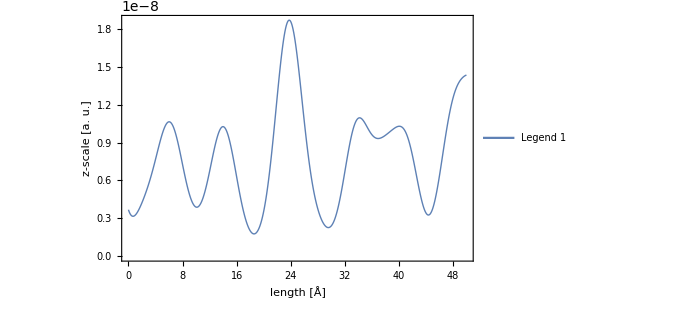

```mathematica
npoints=500;
line=Table[{Norm[(i-1)*(end-start)/(npoints-1)],tmp=(i-1)*(end-start)/(npoints-1)+start;g[tmp[[1]],tmp[[2]]]},{i,npoints}];
lineplot=ListLinePlot[line,Joined->True,PlotRange->Automatic(*{{0.02,1.5*10^1},{-1.5,+1.5}}*),PlotStyle->Thick ,Axes->{False,False},AxesStyle->AbsoluteThickness[2],AxesLabel->(*{,Style["Fermi Level",20,Black]}*)None,AxesOrigin->{0,0},Frame->True,FrameLabel->{"length [Å]","z-scale [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->500,AspectRatio->1/GoldenRatio,Filling->(*{1->0}*)None,FillingStyle->Directive[Orange,Opacity[.5]],PlotLegends->Placed[LineLegend[{"Legend 1","Legend 2","Fermi Level"},LegendLabel->None(*"Legend:"*)(*"NEB image no.:"*),LabelStyle->{Darker[Gray,0.7],FontSize->18},LegendFunction->None],{.75,.75}]]
```

```mathematica
Export["~/Desktop/line_scan_SPM.png",lineplot,Background->None]
```

```mathematica
(* Big preview of the line-path: *)
linecut=Show[spm2D,Graphics[{Thick,Red,Dashed,Line[{start,end}]}]]
```

-Graphics-

```mathematica
Export["~/Desktop/line_path_SPM.png",linecut,Background->None]
```

```mathematica
g=.
line=.
lineplot=.
linecut=.
```

```mathematica
spm2D=.
```